```mathematica
start =1.5;finish=-12;α=0.01;E2=0.95;s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)])+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);
```

```mathematica
Plot[{-E2/(4α)+Abs[s122^2]/(8α nr2),-E2/(4α),Re[-1.(Log[x-I*10^(-5)])+x]/(8α),Im[-1.(Log[-x-I*10^(-5)])+x]/(8α)},{x,start,-7},PlotRange->{-100,170},AspectRatio->1,AxesLabel->{ε/(g V^2),"(log (-ε) + ε)/(8  α); |ψ(ε)|^2"},PlotStyle->{RGBColor[0,1,0],RGBColor[0,1,0],RGBColor[0,0,0],{RGBColor[0,0,0],Dotted}}]
```

```mathematica
Export["figure13.eps",-Graphics-]
```

figure13.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure13.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure13.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figure13.eps"]]]
```

```mathematica
SystemOpen["figure13.eps"]
```

```mathematica
SystemOpen["figure13.eps"]
```

```mathematica
start =25;finish=-30;α=1;E2=-5;s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-5/(x-2+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);
```

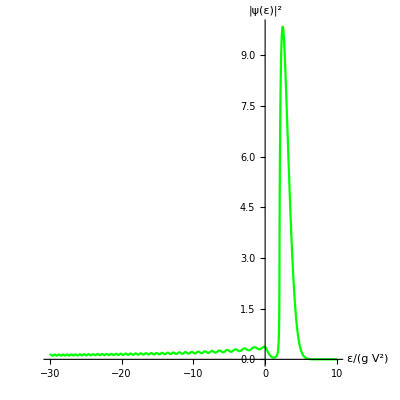

```mathematica
Plot[Abs[s122^2]/(8α nr2),{x,-30,10},PlotRange->All,AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0,1,0]]
```

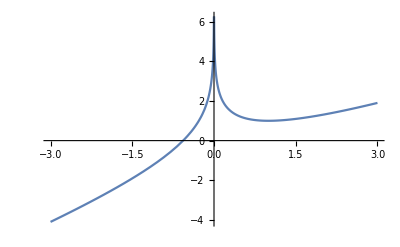

```mathematica
Plot[Re[x-Log[-x+I*10^(-5)]],{x,-3,3}]
```

```mathematica
start =25;finish=-30;α=1;E2=-5;s122=ψ0[x]/.NDSolve[{0== E2 ψ0[x]-α ψ0''[x]+ψ0[x](Log[-x-I*10^(-5)]-10/(x-2+I*10^(-5)))+x ψ0[x],ψ0[start]==0,ψ0'[start]==0.001},ψ0,{x,start,finish}];nr2=(NIntegrate[Abs[s122^2],{x,finish,finish+0.5}]/0.5);
```

Plot[Abs[s122^2]/(8 α nr2),{x,-20,10},PlotRange→All,AspectRatio→1,AxesLabel→{ε/(g V^2),|ψ(ε)|^2},PlotStyle→RGBColor[0.1, 0.1, 0.1],ListPlot[{Callout[{2,0},Spoiler position]},PlotStyle→{Red}]]

```mathematica
Show[Plot[Abs[s122^2]/(8α nr2),{x,-20,10},PlotRange->All,AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0.1,0.1,0.1]],ListPlot[{Callout[{2,0},"Spoiler position"]},PlotStyle->{Red}]]
```

-Graphics-

```mathematica
Export["spoilerstate.eps",-Graphics-]
```

spoilerstate.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["spoilerstate.eps"]]]
```

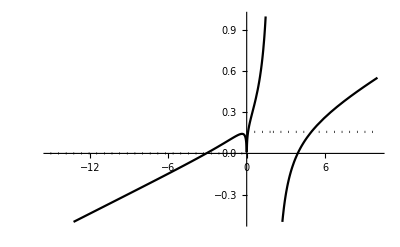

```mathematica
plt5=Plot[{Re[(Log[-x+I*10^(-5)]-10/(x-2+I*10^(-5)))+x]/20,Im[(Log[-x+I*10^(-5)]-10/(x-2+I*10^(-10)))+x]/20},{x,-15,10},PlotRange->{-0.5,1},PlotStyle->{RGBColor[0,0,0],{RGBColor[0,0,0],Dotted}}]
```

```mathematica
Show[Plot[Abs[s122^2]/(8α nr2),{x,-15,10},PlotRange->{-0.5,1},AspectRatio->1,AxesLabel->{ε/(g V^2),"|ψ(ε)|^2"},PlotStyle->RGBColor[0,1,0]],plt5,ListPlot[{Callout[{2,0},"Spoiler position"]},PlotStyle->{Red}]]
```

-Graphics-

```mathematica
Export["spoilerstate.eps",-Graphics-]
```

spoilerstate.eps